```mathematica
fr[n1_,n2_,p1_,p2_,q1_,q2_,f12_]:=1-(2(n1^2 q1 f12))/(2 n1^2 q1 f12+(n1(n1-1))p1+n1 n2 q2)
```

```mathematica
fr[n1_,p1_,q1_,f12_]:=fr[n1,10n1,p1,0.1p1,q1,0.1p1,f12]
```

```mathematica
vol[n1_,p1_,q1_,f12_]:=2 n1^2(p1+q1)+2n1 p1
```

```mathematica
fr[1000,10000,0.001,0.002,0.018,0.0001,0.9]
```

0.0581122

```mathematica
fr[10000,0.0001,0.001,0.15]
```

0.399988

```mathematica
vol[10000,0.0001,0.001,0.5]
```

220002.

Check the spectrums of the dsbm graphs.

```mathematica
Import["~/wc/phd/mathematica/prmGraphs.wl"]
```

```mathematica
data=Import["~/wc/dcpagerank/localgraphclustering/experiments/datasets/dsbm/gdsbm_crafted_2.edgelist"]
```

{{28,6},{82,38},{48,47},{91,95},{139,119},{149,125},{134,185},{200,9929},{200,333},{5290,200},{8501,200},{6287,200},{1277,200},{5977,200},451360,{20199,22523},{20199,23130},{20199,26968},{20199,24921},{20199,28735},{20199,27073},{20199,27168},{20199,21323},{20199,28508},{20199,21691},{26675,20199},{20199,23525},{23790,20199},{20199,28780}}
 |  |  |  |

```mathematica
G=Graph[(#[[1]]->#[[2]])&/@data]
```

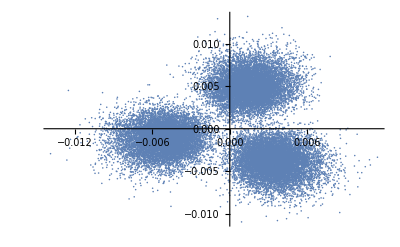

```mathematica
plotSecondComplexEig[G]
```

Eigenvectors::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

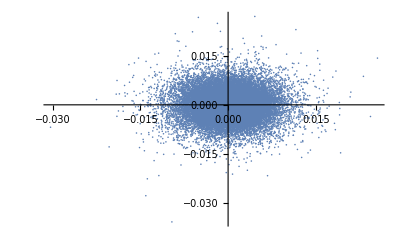

```mathematica
plotComplexEig[hermitianAdjacency[G],3]
```

```mathematica
ns={100,100,1000,1000,1000};
```

```mathematica
ps={0.001,0.001,0.001,0.001,0.001};
```

```mathematica
q={{0,1,0.005,0,0,0},{1,0,0.005,0,0,0},{0.005,0.005,0,0.01,0.01},{0,0,0.01,0,0.01},{0,0,0.01,0.01,0}};
```

```mathematica
f={{0,0.5,0,0,0},{0.5,0,1,0,0},{1,0,0,0.9,0.1},{1,1,0.1,0,0.9},{1,1,0.9,0.1,0}};
```

```mathematica
G2=generalDSBM[ns,ps,q,f]
```

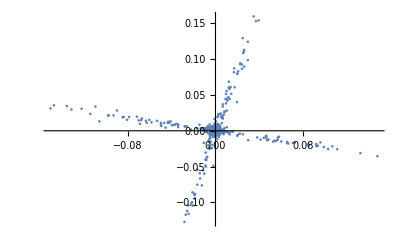

```mathematica
plotSecondComplexEig[G2]
```

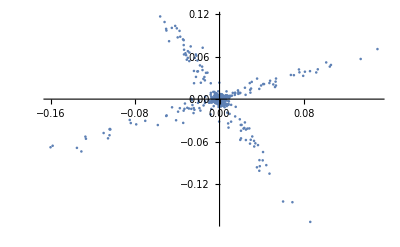

```mathematica
plotComplexEig[hermitianAdjacency[G2],3]
```